```mathematica
SetDirectory [NotebookDirectory[]];
Get["MccPi.m"];
```

```mathematica
SeedRandom[1];
n=100000;

Tocke = MccPi[n];
Tocke //MatrixForm;
```

```mathematica
TockeZnotraj = DeleteCases[Tocke[[All, 1]], {}];
TockeZunaj = DeleteCases[Tocke[[All, 2]], {}];
TockeZnotraj //MatrixForm;
TockeZunaj //MatrixForm;
```

```mathematica
ModulPi[]:=Module[{}, ln=Length[TockeZnotraj]; lz=Length[TockeZunaj];{NumPi = N[ln/(lz+ln) 4, 10], RazPi=Pi-NumPi}]
```

```mathematica
{PriblizekPi, OdstopekPi}=ModulPi[]
```

{3.14204,-0.000447346}

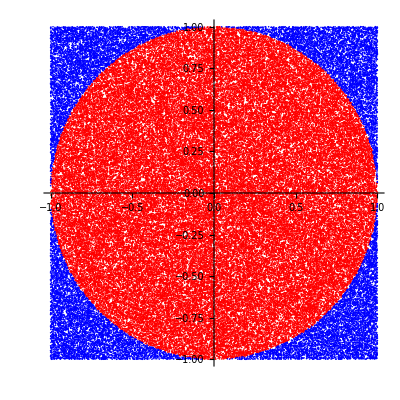

```mathematica
ListPlot[{TockeZnotraj, TockeZunaj}, AspectRatio->1, PlotRange->{{-1, 1}, {-1, 1}}, PlotStyle->{{Red}, {Blue}}]
```